```mathematica
kHz = 10^3;
Hz=1;
ωz = 2*π*710*kHz;
```

## Two ions - mixed species

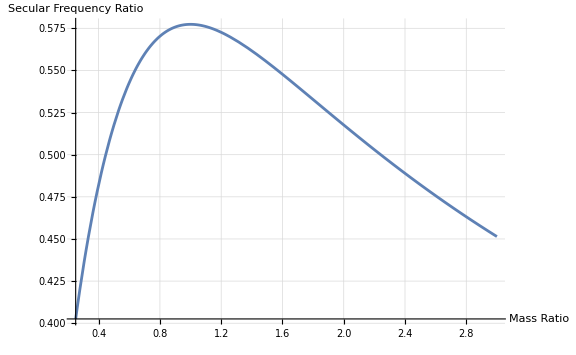

```mathematica
Ωm[μ_, ωz_] := Sqrt[(1+μ-Sqrt[1-μ+μ^2])/μ]*ωz
Ωp[μ_, ωz_] := Sqrt[(1+μ+Sqrt[1-μ+μ^2])/μ]*ωz
Plot[Ωm[μ, ωz]/Ωp[μ, ωz], {μ, 0.25,3},
AxesLabel->{Style["Mass Ratio", 16], Style["Secular Frequency Ratio", 16]},
GridLines->Automatic,
ImageSize->Large, TicksStyle->Directive["Label", 16]]
```

## Three ions - mixed species (2 bright, 1 dark)

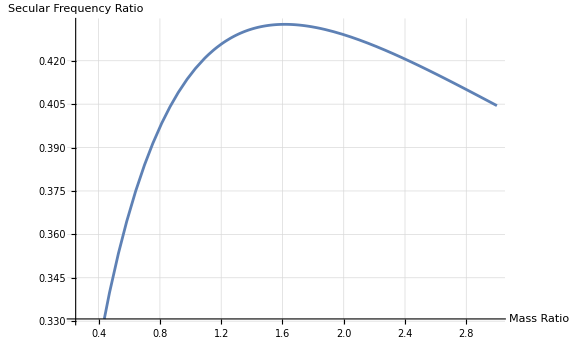

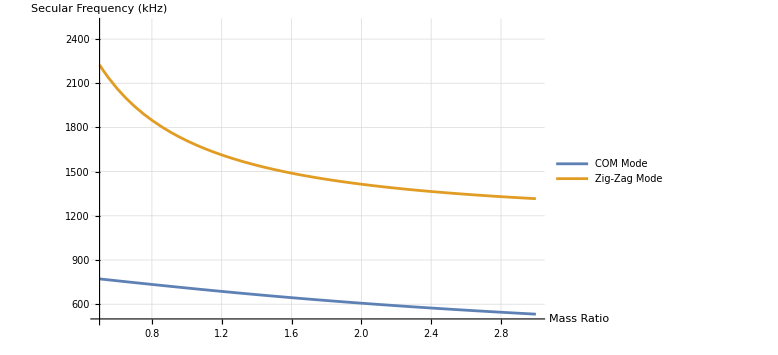

```mathematica
η1[μ_, ωz_]:= ωz*Sqrt[13/10+1/(10μ)(21-Sqrt[441-34μ+169 μ^2])];
η3[μ_, ωz_]:= ωz*Sqrt[13/10+1/(10μ)(21+Sqrt[441-34μ+169 μ^2])];
Plot[η1[μ, ωz]/η3[μ, ωz], {μ,0.25,3},
AxesLabel->{Style["Mass Ratio", 16], Style["Secular Frequency Ratio", 16]},
GridLines->Automatic,
ImageSize->Large, TicksStyle->Directive["Label", 16]]
MixedModesSec = Plot[{η1[μ, ωz]/(2*π*kHz), η3[μ, ωz]/(2*π*kHz)}, {μ,0.5,3}, 
AxesLabel->{Style["Mass Ratio", 16], Style["Secular Frequency (kHz)", 16]}, PlotLegends->{"COM Mode", "Zig-Zag Mode"},
PlotRange->{500,2500},  GridLines->Automatic,
ImageSize->Large, TicksStyle->Directive["Label", 16]]
(*Export["\\\\eric.physics.ucla.edu\\groups\\motion\\Posters and Presentations\\Josh\\ATC\\images\\simulation_images\\mixedModeSec.svg", MixedModesSec];*)
```

```mathematica
N[{1/Sqrt[1+(Sqrt[μ]/8(13-5*η1[μ,1]^2))^2+1]+1/Sqrt[1+(Sqrt[μ]/8(13-5*η1[μ,1]^2))^2+1]}/.{μ->36/40}]
```

```mathematica
{1.1821733886544934}
N[2/Sqrt[3]]
```

{1.18217}

1.1547

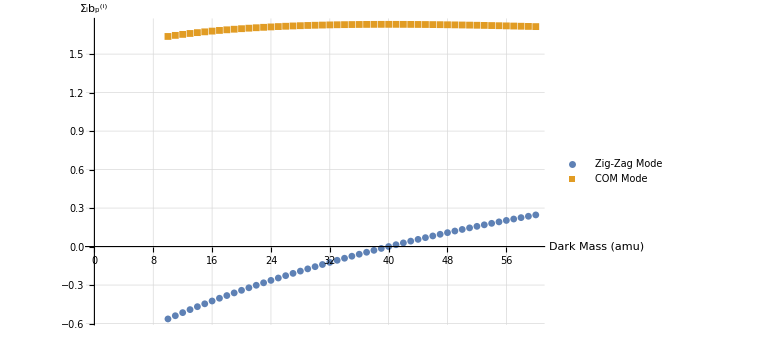

```mathematica
ComVec[μ_]:= {1/Sqrt[1+(Sqrt[μ]/8(13-5*η1[μ,1]^2))^2+1],(Sqrt[μ]/8(13-5*η1[μ,1]^2))/Sqrt[1+(Sqrt[μ]/8(13-5*η1[μ,1]^2))^2+1],1/Sqrt[1+(Sqrt[μ]/8(13-5*η1[μ,1]^2))^2+1]};
ZigVec[μ_]:= {1/Sqrt[1+(Sqrt[μ]/8(13-5*η3[μ,1]^2))^2+1],(Sqrt[μ]/8(13-5*η3[μ, 1]^2))/Sqrt[1+(Sqrt[μ]/8(13-5*η3[μ,1]^2))^2+1],1/Sqrt[1+(Sqrt[μ]/8(13-5*η3[μ,1]^2))^2+1]};
masses = Range[10,60];
modeCoupling = ZigVec[masses/40];
modeCouplingDarkMass = ListPlot[{Thread[{masses, Total[ZigVec[masses/40]]}], Thread[{masses, Total[ComVec[masses/40]]}]},
AxesLabel->{Style["Dark Mass (amu)", 16], Style["Σ_ib_p^(i)", 16]}, PlotLegends->{"Zig-Zag Mode", "COM Mode"}, 
PlotMarkers->{Automatic, Small}, GridLines->Automatic,
ImageSize->Large, TicksStyle->Directive["Label", 16]]
Export["\\\\eric.physics.ucla.edu\\groups\\motion\\Posters and Presentations\\Josh\\ATC\\images\\simulation_images\\modeCouplingDarkMass.svg", modeCouplingDarkMass];
```

```mathematica
N[Total[ZigVec[10/40]]]
```

-2.84988

```mathematica
FullSimplify[Solve[η1[μ, ωz]/η3[μ, ωz]== 0.7/1.7, μ]];
sols = FullSimplify[Solve[η1[μ, ωz]/η3[μ, ωz]== R, μ]];
f = sols[[1]][[1]][[2]]/.{R->ω1/ω3};
σμ = FullSimplify[Sqrt[(D[f, ω1])^2 Subscript[σ, ω1]^2+(D[f, ω3])^2 Subscript[σ, ω3]^2+2*D[f, ω1]*D[f, ω3]*0]];
(*σμ = Abs[ω1/ω3]*Sqrt[(Subscript[σ, ω1]/ω1)^2+(Subscript[σ, ω3]/ω3)^2];*)
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

```mathematica
(*Allen Dev Parameters*)
comMode = 721.35*kHz;
comModeDetuning = 1.98*Hz;
zigMode = 1770.575*kHz;
zigModeDetuning = -38.18*Hz;
mCaAmu = 39.96204;
mCaAmu * (sols[[1]][[1]][[2]]/.{R->(comMode+comModeDetuning)/(zigMode+zigModeDetuning)})
σμ = FullSimplify[Sqrt[(D[f, ω1])^2 Subscript[σ, ω1]^2+(D[f, ω3])^2 Subscript[σ, ω3]^2+2*D[f, ω1]*D[f, ω3]*0]];
mCaAmu*σμ/.{ω1->2π*(comMode+comModeDetuning), ω3->2*π*(zigMode+zigModeDetuning), Subscript[σ, ω1]->0.98*2*π,Subscript[σ, ω3]->2.3*2*π}
```

35.9751

0.000341346